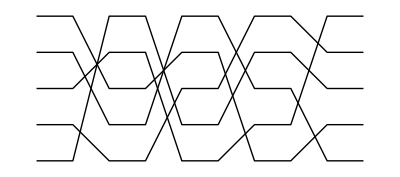

```mathematica
compactBraid={{1,5,2,4,3},{2,1,3,5,4},{3,4,1,2,5},{4,2,5,3,1}, {5,3,4,1,2}};
showBraid@compactBraid
```

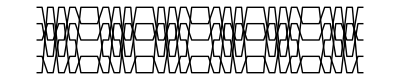

```mathematica
longBraid=Flatten[Table[{#,Reverse[#]},{3}]]&/@compactBraid;
showBraid@longBraid
```

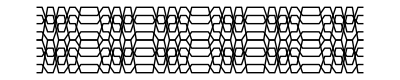

```mathematica
wideBraid=Join[longBraid+4,longBraid];
showBraid@wideBraid
```

```mathematica
seq=RandomSample[Range[5]]
```

{2,1,3,4,5}

```mathematica
cord[seq_]:=Block[{pos2,fn},seq2=Riffle[seq,seq];fn[y_,{x_}]:={x,y};MapIndexed[fn,seq2]]
```

```mathematica
showCord[seq_]:=Graphics@Line@cord[seq]
```

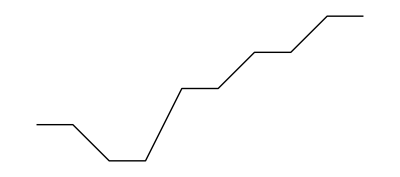

```mathematica
pattern = showCord[seq]
```

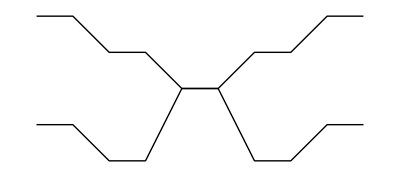

```mathematica
Show@{showCord[seq],showCord[Reverse[seq]]}
```

```mathematica
longCord=Flatten[Table[{#,Reverse[#]},{3}]]&/@pattern;
showCord@longCord
```

Riffle::list: List expected at position 1 in GraphicsBox[List[LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]]]], GraphicsBox[List[LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]], LineBox[List[List[1, 2], List[2, 2], List[3, 1], List[4, 1], List[5, 3], List[6, 3], List[7, 4], List[8, 4], List[9, 5], List[10, 5]]]]].

-Graphics-